# Leading order cross section for qq̄→(χ̃)_i^0(χ̃)_j^±

## Initialisation

Load FeynCalc and FeynArts. Furthermore, this notebook makes use of three packages found in the “include” folder.

```mathematica
description = "Leading order cross section of neutralino and chargino pair production at parton level.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose = 0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
$EwinoRoot = ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$EwinoRoot, "include"}]];
<< XSec`
<< EWinos`
<< CalcTools`
```

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

```mathematica
ResultsDir = FileNameJoin[{$EwinoRoot, "results", "LO"}];
```

## Generate Feynman diagrams and amplitudes

Some text

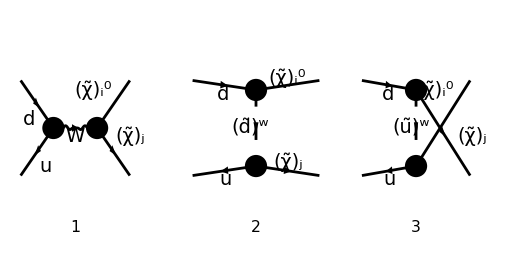

```mathematica
treeDiagrams = InsertFields[
	CreateTopologies[0, 2 -> 2, ExcludeTopologies -> {Boxes,SelfEnergies,Tadpoles}], 
	{F[4, {1, a}], -F[3, {1, b}]} -> {F[11, {i}], F[12, {j}]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling,NoElectronHCoupling},
	ExcludeParticles -> {F[11],F[12],S[1],S[2],S[3],S[4]}
];
Paint[treeDiagrams, Numbering->Simple, ColumnsXRows -> {3, 1}, ImageSize->{512,256}];
```

```mathematica
M0[0] = FCFAConvert[
	CreateFeynAmp[treeDiagrams], 
	IncomingMomenta -> {ki,kj},
	OutgoingMomenta -> {pi,pj},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> True,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ,ν},
	FinalSubstitutions -> AmpSimplifyRules
]/.{IndexDelta -> FeynCalc`IndexDelta};
```

```mathematica
tempPrefactor = SMP["g_W"]^2 FeynCalc`IndexDelta[a,b];
M0[1] = tempPrefactor*DiracSimplify /@ (Convert2QZCharges /@ (M0[0]/tempPrefactor));
M0[2] = M0[1] //. SuperChargeRules;
Clear[tempPrefactor]
```

```mathematica
Ms[0] = Part[M0[0], 1] //. WSimplifyRules /. FeynCalc`IndexDelta[i,j] -> 3/2 Qe FeynCalc`IndexDelta[i,j] // Simplify
Mt[0] = Part[M0[0], 2] /. SMP["V_ud", ⅈ] -> CKM[1,1] //. QSimplifyRules // Simplify
Mu[0] = Part[M0[0], 3] /. SMP["V_ud", ⅈ] -> CKM[1,1] //. QSimplifyRules // Simplify
```

-(g^μν (φ(p_j,m_j)).(-ⅈ g_W (γ^ν.(γ̄)^6 O_ij^L+γ^ν.(γ̄)^7 O_ij^R)).(φ(-p_i,m_i)) (φ(-k_j)).(ⅈ g_W γ^μ.(γ̄)^7 δ_ab C_(q q' W)^L).(φ(k_i)))/((p_i+p_j)^2-m_W^2)

((φ(p_i,m_i)).(-ⅈ √2 g_W ((γ̄)^7 Conjugate[(C_(d(d̃)_Sfe5(χ̃)_i^0)^L)]+(γ̄)^6 Conjugate[(C_(d(d̃)_Sfe5(χ̃)_i^0)^R)])).(φ(k_i)) (φ(-k_j)).(-ⅈ √2 (γ̄)^6 g_W δ_ab C_(u(d̃)_Sfe5(χ̃)_j^±)^L).(φ(-p_j,m_j)))/((p_j-k_j)^2-m_((d̃)_(1,Sfe5))^2)

-((φ(p_j,m_j)).(-ⅈ √2 (γ̄)^7 g_W Conjugate[(C_(d(ũ)_Sfe5(χ̃)_j^±)^L)]).(φ(k_i)) (φ(-k_j)).(-ⅈ √2 g_W δ_ab ((γ̄)^6 C_(u(ũ)_Sfe5(χ̃)_i^0)^L+(γ̄)^7 C_(u(ũ)_Sfe5(χ̃)_i^0)^R)).(φ(-p_i,m_i)))/((p_i-k_j)^2-m_((ũ)_(1,Sfe5))^2)

Divide the three amplitudes into separate channels and convert to Q_A^XY and Z_s^X supercharges.

```mathematica
Ms[1] = (Ms[0] // FeynAmpDenominatorExplicit) /. SMP["m_W"]^2->DW
Mt[1] = (Mt[0] // FeynAmpDenominatorExplicit) /. Index[Sfermion,5]->A
Mu[1] = (Mu[0] // FeynAmpDenominatorExplicit) /. Index[Sfermion,5]->A

MsC[1] = ConjugateAmplitude[Ms[1]]/.{A->B,μ->ρ,ν->σ};
MtC[1] = ConjugateAmplitude[Mt[1]]/.{A->B,μ->ρ,ν->σ};
MuC[1] = ConjugateAmplitude[Mu[1]]/.{A->B,μ->ρ,ν->σ};
```

-(g^μν (φ(p_j,m_j)).(-ⅈ g_W (γ^ν.(γ̄)^6 O_ij^L+γ^ν.(γ̄)^7 O_ij^R)).(φ(-p_i,m_i)) (φ(-k_j)).(ⅈ g_W γ^μ.(γ̄)^7 δ_ab C_(q q' W)^L).(φ(k_i)))/(s-Δ_W)

((φ(p_i,m_i)).(-ⅈ √2 g_W ((γ̄)^7 Conjugate[(C_(d(d̃)_A(χ̃)_i^0)^L)]+(γ̄)^6 Conjugate[(C_(d(d̃)_A(χ̃)_i^0)^R)])).(φ(k_i)) (φ(-k_j)).(-ⅈ √2 (γ̄)^6 g_W δ_ab C_(u(d̃)_A(χ̃)_j^±)^L).(φ(-p_j,m_j)))/(t-m_((d̃)_(1,A))^2)

-((φ(p_j,m_j)).(-ⅈ √2 (γ̄)^7 g_W Conjugate[(C_(d(ũ)_A(χ̃)_j^±)^L)]).(φ(k_i)) (φ(-k_j)).(-ⅈ √2 g_W δ_ab ((γ̄)^6 C_(u(ũ)_A(χ̃)_i^0)^L+(γ̄)^7 C_(u(ũ)_A(χ̃)_i^0)^R)).(φ(-p_i,m_i)))/(u-m_((ũ)_(1,A))^2)

Save results in “results/LO/NCamps.m”
They can be loaded with
LOAmps=Import[FileNameJoin[{ResultsDir,"NCamps.m"}]];
which creates a list containing the s, t, u amplitudes followed by their conjugates in the same order.

```mathematica
Export[FileNameJoin[{ResultsDir, "NCamps.m"}], ToString/@FullForm/@{Ms[0],Mt[0],Mu[0],MsC[0],MtC[0],MuC[0]}];
```

## Differential Cross-Section

Some more text

```mathematica
Iss[0] = SquareAmplitudes[Ms[1],MsC[1]];
Itt[0] = SquareAmplitudes[Mt[1],MtC[1]];
Iuu[0] = SquareAmplitudes[Mu[1],MuC[1]];
Ist[0] = (SquareAmplitudes[Ms[1],MtC[1]/.B->A]+SquareAmplitudes[Mt[1],MsC[1]])/2;
Isu[0] = (SquareAmplitudes[Ms[1],MuC[1]/.B->A]+SquareAmplitudes[Mu[1],MsC[1]])/2;
Itu[0] = (SquareAmplitudes[Mt[1],MuC[1]]+SquareAmplitudes[Mu[1]/.A->B,MtC[1]/.B->A])/2;
```

Convert the dimension D→4.

```mathematica
Iss[1] = FixDimension[Iss[0]/.Convert2Den];
Itt[1] = FixDimension[Itt[0]/.Convert2Den];
Iuu[1] = FixDimension[Iuu[0]/.Convert2Den];
Ist[1] = FixDimension[Ist[0]/.Convert2Den];
Isu[1] = FixDimension[Isu[0]/.Convert2Den];
Itu[1] = FixDimension[Itu[0]/.Convert2Den];
```

Draw out common prefactor between the squared amplitudes and factor them in terms of denominators and basic kinematic terms.

```mathematica
CommonPrefactor = 4 (FeynCalc`IndexDelta[a,b])^2 SMP["g_W"]^4;
Iss[2] = CommonPrefactor FactorDenominators[Iss[1]/CommonPrefactor];
Itt[2] = CommonPrefactor FactorDenominators[Itt[1]/CommonPrefactor];
Iuu[2] = CommonPrefactor FactorDenominators[Iuu[1]/CommonPrefactor];
Ist[2] = CommonPrefactor FactorDenominators[Ist[1]/CommonPrefactor];
Isu[2] = CommonPrefactor FactorDenominators[Isu[1]/CommonPrefactor];
Itu[2] = CommonPrefactor FactorDenominators[Itu[1]/CommonPrefactor];
```

We can convert these to  Q_A^XY and Z_s^X supercharges, and write them out in a nice form using this.

```mathematica
CommonPrefactor Collect[
	Expand[Itt[2]/CommonPrefactor] //. SuperChargeRules,
	{s*MEW[i]*MEW[j],(t-MEW[i]^2)(t-MEW[j]^2),(u-MEW[i]^2)(u-MEW[j]^2),t*u-MEW[i]^2*MEW[j]^2},
	Simplify
]
```

4 g_W^4 δ_ab^2 (t-m_i^2) (t-m_j^2) 1/(t-m_((d̃)_(1,A))^2) 1/(t-m_((d̃)_(1,B))^2) (Q_(d̃ B)^RL Conjugate[(Q_(d̃A)^RL)]+Q_(d̃ B)^LL Conjugate[(Q_(d̃A)^LL)])

Add all squared amplitudes, omitting the common prefactor.

```mathematica
Itot[0] = (Iss[2]+Itt[2]+Iuu[2]+2Ist[2]+2Isu[2]+2Itu[2])/CommonPrefactor;
Itot[1] = Collect[
	Itot[0],
	{s*MEW[i]*MEW[j],(t-MEW[i]^2)(t-MEW[j]^2),(u-MEW[i]^2)(u-MEW[j]^2),t*u-MEW[i]^2*MEW[j]^2},
	(Collect2[
		#1,
		Den[args1__]Den[args2__],
		Factoring -> (FullSimplify[Expand[#]//.SuperChargeRules]&)
	]&)
];
```

Show that the total amplitude can be written as effective charges in front of four different kinematic terms.

```mathematica
Collect[
	Itot[1],
	{s*MEW[i]*MEW[j],(t-MEW[i]^2)(t-MEW[j]^2),(u-MEW[i]^2)(u-MEW[j]^2),t*u-MEW[i]^2*MEW[j]^2},
	(CollectEffCharges[Expand[#]]&)
]
```

(u-m_i^2) (u-m_j^2) (-KK(523) (Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL+Q_(ũ A)^LL Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)])+Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2+KK(525) (Q_(ũ A)^RL Conjugate[(Q_(ũB)^RL)]+Q_(ũ A)^LL Conjugate[(Q_(ũB)^LL)]))+s m_i m_j (KK(522) (Conjugate[(Q_(d̃A)^LL)] Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)]+Q_(d̃ A)^LL W_((χ̃)_i^0(χ̃)_j^±)^LL)-KK(523) (Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LR+Q_(ũ A)^LL Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)])+W_((χ̃)_i^0(χ̃)_j^±)^LL Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)]+Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LR-KK(521) (Conjugate[(Q_(d̃A)^LL)] Conjugate[(Q_(ũB)^LL)]+Q_(d̃ A)^LL Q_(ũ B)^LL))+(t-m_i^2) (t-m_j^2) (KK(522) (Conjugate[(Q_(d̃A)^LL)] Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)]+Q_(d̃ A)^LL W_((χ̃)_i^0(χ̃)_j^±)^LR)+W_((χ̃)_i^0(χ̃)_j^±)^LR Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)]+KK(524) (Q_(d̃ B)^RL Conjugate[(Q_(d̃A)^RL)]+Q_(d̃ B)^LL Conjugate[(Q_(d̃A)^LL)]))

Calculate the total differential cross section and save to “results/LO/NCdxsec.m”

```mathematica
DiffXSecPrefactor = CommonPrefactor/(64 Pi CA^2 s^2) /. {(FeynCalc`IndexDelta[a,b])^p_->CA,SMP["g_W"]->Sqrt[4π alphaW]};
DiffXSec = DiffXSecPrefactor Itot[1] /. {(FeynCalc`IndexDelta[a,b])^p_->CA,SMP["g_W"]->Sqrt[4π alphaW]}

Export[FileNameJoin[{ResultsDir, "NCdxsec.m"}], FullForm[DiffXSec]//ToString];
```

1/(s^2 C_A)π α_W^2 ((u-m_i^2) (u-m_j^2) (1/(u-m_((ũ)_(1,A))^2) (-Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL-Q_(ũ A)^LL Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)]+1/(u-m_((ũ)_(1,B))^2) (Q_(ũ A)^RL Conjugate[(Q_(ũB)^RL)]+Q_(ũ A)^LL Conjugate[(Q_(ũB)^LL)]))+Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2)+s m_i m_j (-1/(t-m_((d̃)_(1,A))^2) (1/(u-m_((ũ)_(1,B))^2) (Conjugate[(Q_(d̃A)^LL)] Conjugate[(Q_(ũB)^LL)]+Q_(d̃ A)^LL Q_(ũ B)^LL)-Q_(d̃ A)^LL W_((χ̃)_i^0(χ̃)_j^±)^LL)+Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] (W_((χ̃)_i^0(χ̃)_j^±)^LR+1/(t-m_((d̃)_(1,A))^2) Conjugate[(Q_(d̃A)^LL)])-1/(u-m_((ũ)_(1,A))^2) (Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LR+Q_(ũ A)^LL Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)])+W_((χ̃)_i^0(χ̃)_j^±)^LL Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)])+(t-m_i^2) (t-m_j^2) 1/(t-m_((d̃)_(1,A))^2) (Conjugate[(Q_(d̃A)^LL)] (Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)]+Q_(d̃ B)^LL 1/(t-m_((d̃)_(1,B))^2))+1/(t-m_((d̃)_(1,B))^2) Q_(d̃ B)^RL Conjugate[(Q_(d̃A)^RL)])+(t-m_i^2) (t-m_j^2) W_((χ̃)_i^0(χ̃)_j^±)^LR (Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)]+Q_(d̃ A)^LL 1/(t-m_((d̃)_(1,A))^2)))

```mathematica
DiffXSecPrefactor Collect[
	ReplaceAll[DiffXSec/DiffXSecPrefactor, {DSf[args__]->MSf[args]^2(*, DZ->SMP["m_Z"]^2*), DSfC[args__]->MSf[args]^2}],
	{s*MEW[i]*MEW[j],(t-MEW[i]^2)(t-MEW[j]^2),(u-MEW[i]^2)(u-MEW[j]^2),t*u-MEW[i]^2*MEW[j]^2},
	(FRH[CollectEffCharges[Expand[#]]]&)
] // Refine[#, Assumptions->{SMP[_]∈Reals, MSf[__]∈Reals}]&;
% //. {a_+a_* -> 2Re[a], a_ b_+a_*b_* -> 2Re[a b], a_ b_*+a_*b_ -> 2Re[a b*], a_^2+a_*^2 -> 2Re[a^2]}
```

1/(s^2 C_A)π α_W^2 ((u-m_i^2) (u-m_j^2) (-2 1/(u-m_((ũ)_(1,A))^2) Re(Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL)+Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2+1/(u-m_((ũ)_(1,A))^2) 1/(u-m_((ũ)_(1,B))^2) (Q_(ũ A)^RL Conjugate[(Q_(ũB)^RL)]+Q_(ũ A)^LL Conjugate[(Q_(ũB)^LL)]))+s m_i m_j (-2 1/(u-m_((ũ)_(1,A))^2) Re(Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LR)+2 1/(t-m_((d̃)_(1,A))^2) Re(Q_(d̃ A)^LL W_((χ̃)_i^0(χ̃)_j^±)^LL)+2 Re(W_((χ̃)_i^0(χ̃)_j^±)^LL Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)])-2 1/(t-m_((d̃)_(1,A))^2) 1/(u-m_((ũ)_(1,B))^2) Re(Q_(d̃ A)^LL Q_(ũ B)^LL))+(t-m_i^2) (t-m_j^2) (2 1/(t-m_((d̃)_(1,A))^2) Re(Q_(d̃ A)^LL W_((χ̃)_i^0(χ̃)_j^±)^LR)+W_((χ̃)_i^0(χ̃)_j^±)^LR Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)]+1/(t-m_((d̃)_(1,A))^2) 1/(t-m_((d̃)_(1,B))^2) (Q_(d̃ B)^RL Conjugate[(Q_(d̃A)^RL)]+Q_(d̃ B)^LL Conjugate[(Q_(d̃A)^LL)])))

Printing the individual contributions to the differential cross-section.

```mathematica
WXsecDiff = DiffXSecPrefactor (DiffXSec/DiffXSecPrefactor /. Qtu[_][__][__] -> 0 // CollectEffCharges // FRH)
SqXSecDiff = DiffXSecPrefactor (DiffXSec/DiffXSecPrefactor /. Wij[_][__] -> 0 // CollectEffCharges // FRH)
InterferenceXSecDiff = DiffXSecPrefactor (DiffXSec / DiffXSecPrefactor //. 
	{Wij[_][__]^2 -> 0, Abs[Wij[_][__]] -> 0, Wij[_][__]*^2 -> 0,
	Qtu[_][__][args1__]Qtu[_][__][args2__] -> 0, Qtu[_][__][args1__]Qtu[_][__][args2__]* -> 0,
	Qtu[_][__][args1__]*Qtu[_][__][args2__]* -> 0}  // CollectEffCharges // FRH)
```

(π α_W^2 ((u-m_i^2) (u-m_j^2) Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2+s m_i m_j (W_((χ̃)_i^0(χ̃)_j^±)^LL Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)]+Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LR)+(t-m_i^2) (t-m_j^2) W_((χ̃)_i^0(χ̃)_j^±)^LR Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)]))/(s^2 C_A)

(π α_W^2 (-s m_i m_j 1/(t-m_((d̃)_(1,A))^2) 1/(u-m_((ũ)_(1,B))^2) (Conjugate[(Q_(d̃A)^LL)] Conjugate[(Q_(ũB)^LL)]+Q_(d̃ A)^LL Q_(ũ B)^LL)+(t-m_i^2) (t-m_j^2) 1/(t-m_((d̃)_(1,A))^2) 1/(t-m_((d̃)_(1,B))^2) (Q_(d̃ B)^RL Conjugate[(Q_(d̃A)^RL)]+Q_(d̃ B)^LL Conjugate[(Q_(d̃A)^LL)])+(u-m_i^2) (u-m_j^2) 1/(u-m_((ũ)_(1,A))^2) 1/(u-m_((ũ)_(1,B))^2) (Q_(ũ A)^RL Conjugate[(Q_(ũB)^RL)]+Q_(ũ A)^LL Conjugate[(Q_(ũB)^LL)])))/(s^2 C_A)

1/(s^2 C_A)π α_W^2 ((t-m_i^2) (t-m_j^2) 1/(t-m_((d̃)_(1,A))^2) Conjugate[(Q_(d̃A)^LL)] (Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)]+Q_(d̃ B)^LL 1/(t-m_((d̃)_(1,B))^2))+s m_i m_j Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] (W_((χ̃)_i^0(χ̃)_j^±)^LR+1/(t-m_((d̃)_(1,A))^2) Conjugate[(Q_(d̃A)^LL)])+(t-m_i^2) (t-m_j^2) W_((χ̃)_i^0(χ̃)_j^±)^LR (Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)]+Q_(d̃ A)^LL 1/(t-m_((d̃)_(1,A))^2))-s m_i m_j 1/(u-m_((ũ)_(1,A))^2) (Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LR+Q_(ũ A)^LL Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)])-(u-m_i^2) (u-m_j^2) 1/(u-m_((ũ)_(1,A))^2) (Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL+Q_(ũ A)^LL Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)])+s m_i m_j Q_(d̃ A)^LL 1/(t-m_((d̃)_(1,A))^2) W_((χ̃)_i^0(χ̃)_j^±)^LL+s m_i m_j W_((χ̃)_i^0(χ̃)_j^±)^LL Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)])

## Integrated Cross-Section

Some text.

To simplify before integrating over t, we will need to convert all terms containing u to t .
Furthermore, it will simplify the expression somewhat to convert to the supercharges Q_A^XY and Z_s^X.

```mathematica
$Assumptions = {
	(tMass|uMass)[__] ∈ Reals,
	SMP[_] ∈ Reals
};
```

```mathematica
Itot[2] = Collect2[
	Itot[1] /. {Den[u,MSf[args__]^2] -> -Den[t,uMass[args]],Den[t,MSf[args__]^2] -> Den[t,tMass[args]]} /. {u -> MEW[i]^2+MEW[j]^2-s-t} // Expand,
	Den[args1__]Den[args2__],
	Factoring -> Simplify
];
```

Convert all t-dependence to a dictionary of standard t-integrals T_d^p(Δ_1,...,Δ_d).

```mathematica
ItotIntegrals[0] = ToTIntegrals[Itot[2]] // Refine[#, Assumptions -> (tMass|uMass)[__] ∈ Reals]&
ItotIntegrals[1] = ReduceTIntegrals[ItotIntegrals[0]];
```

KK(554) T_2^0(Δ_((d̃)_(1,A))^t,Δ_((ũ)_(1,B))^u)+KK(544) T_2^0(Δ_((d̃)_(1,A))^t,Δ_((d̃)_(1,B))^t)+KK(550) T_2^1(Δ_((d̃)_(1,A))^t,Δ_((d̃)_(1,B))^t)+KK(566) T_2^2(Δ_((d̃)_(1,A))^t,Δ_((d̃)_(1,B))^t)+KK(560) T_2^0(Δ_((ũ)_(1,A))^u,Δ_((ũ)_(1,B))^u)+KK(556) T_2^1(Δ_((ũ)_(1,A))^u,Δ_((ũ)_(1,B))^u)+KK(552) T_2^2(Δ_((ũ)_(1,A))^u,Δ_((ũ)_(1,B))^u)+KK(558) T_1^0(Δ_((d̃)_(1,A))^t)+KK(564) T_1^1(Δ_((d̃)_(1,A))^t)+KK(562) T_1^2(Δ_((d̃)_(1,A))^t)+KK(546) T_1^0(Δ_((ũ)_(1,A))^u)+KK(574) T_1^1(Δ_((ũ)_(1,A))^u)+KK(572) T_1^2(Δ_((ũ)_(1,A))^u)+KK(570) T_0^0+KK(548) T_0^1+KK(568) T_0^2

We can write it out in terms of the basic charges using GetKinematicCoefficients .

```mathematica
Collect2[ItotIntegrals[0], tIntegral[__], Factoring -> GetKinematicCoefficients]
```

m_i^2 T_2^0(Δ_((d̃)_(1,A))^t,Δ_((d̃)_(1,B))^t) (Conjugate[(Q_(d̃A)^LL)] Q_(d̃ B)^LL+Conjugate[(Q_(d̃A)^RL)] Q_(d̃ B)^RL) m_j^2+s m_i T_2^0(Δ_((d̃)_(1,A))^t,Δ_((ũ)_(1,B))^u) (Conjugate[(Q_(ũB)^LL)] Conjugate[(Q_(d̃A)^LL)]+Q_(ũ B)^LL Q_(d̃ A)^LL) m_j+(2 s Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2+(-Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2-Abs[W_((χ̃)_i^0(χ̃)_j^±)^LR]^2) m_i^2+(-Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2-Abs[W_((χ̃)_i^0(χ̃)_j^±)^LR]^2) m_j^2) T_0^1+(Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2+Abs[W_((χ̃)_i^0(χ̃)_j^±)^LR]^2) T_0^2+T_0^0 (s^2 Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2-s m_i^2 Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2-s m_j^2 Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2+(Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2+Abs[W_((χ̃)_i^0(χ̃)_j^±)^LR]^2) m_i^2 m_j^2+s m_i m_j (Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)] W_((χ̃)_i^0(χ̃)_j^±)^LL+Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LR))+T_1^2(Δ_((ũ)_(1,A))^u) (Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL+Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] Q_(ũ A)^LL)+T_1^1(Δ_((ũ)_(1,A))^u) ((-Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL-Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] Q_(ũ A)^LL) m_i^2+m_j^2 (-Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL-Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] Q_(ũ A)^LL)+s (2 Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL+2 Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] Q_(ũ A)^LL))+T_1^0(Δ_((ũ)_(1,A))^u) ((Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL+Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] Q_(ũ A)^LL) s^2+m_i^2 (-Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL-Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] Q_(ũ A)^LL) s+m_j^2 (-Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL-Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] Q_(ũ A)^LL) s+m_i m_j (Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LR+Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)] Q_(ũ A)^LL) s+m_i^2 m_j^2 (Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL+Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] Q_(ũ A)^LL))+T_2^2(Δ_((ũ)_(1,A))^u,Δ_((ũ)_(1,B))^u) (Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL)+T_2^0(Δ_((ũ)_(1,A))^u,Δ_((ũ)_(1,B))^u) ((Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL) s^2+m_i^2 (-Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL-Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL) s+m_j^2 (-Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL-Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL) s+m_i^2 m_j^2 (Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL))+T_2^1(Δ_((ũ)_(1,A))^u,Δ_((ũ)_(1,B))^u) ((-Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL-Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL) m_i^2+m_j^2 (-Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL-Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL)+s (2 Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+2 Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL))+T_1^2(Δ_((d̃)_(1,A))^t) (Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)] Conjugate[(Q_(d̃A)^LL)]+W_((χ̃)_i^0(χ̃)_j^±)^LR Q_(d̃ A)^LL)+T_1^1(Δ_((d̃)_(1,A))^t) ((-Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)] Conjugate[(Q_(d̃A)^LL)]-W_((χ̃)_i^0(χ̃)_j^±)^LR Q_(d̃ A)^LL) m_i^2+m_j^2 (-Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)] Conjugate[(Q_(d̃A)^LL)]-W_((χ̃)_i^0(χ̃)_j^±)^LR Q_(d̃ A)^LL))+T_1^0(Δ_((d̃)_(1,A))^t) (m_i^2 (Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)] Conjugate[(Q_(d̃A)^LL)]+W_((χ̃)_i^0(χ̃)_j^±)^LR Q_(d̃ A)^LL) m_j^2+s m_i (Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] Conjugate[(Q_(d̃A)^LL)]+W_((χ̃)_i^0(χ̃)_j^±)^LL Q_(d̃ A)^LL) m_j)+T_2^2(Δ_((d̃)_(1,A))^t,Δ_((d̃)_(1,B))^t) (Conjugate[(Q_(d̃A)^LL)] Q_(d̃ B)^LL+Conjugate[(Q_(d̃A)^RL)] Q_(d̃ B)^RL)+T_2^1(Δ_((d̃)_(1,A))^t,Δ_((d̃)_(1,B))^t) ((-Conjugate[(Q_(d̃A)^LL)] Q_(d̃ B)^LL-Conjugate[(Q_(d̃A)^RL)] Q_(d̃ B)^RL) m_i^2+m_j^2 (-Conjugate[(Q_(d̃A)^LL)] Q_(d̃ B)^LL-Conjugate[(Q_(d̃A)^RL)] Q_(d̃ B)^RL))

Write out the analytic results for all the T_d^p-integrals and collect into the possible terms dependent on the t-limits t1 and t0.

```mathematica
ItotIntegrals[2] = Collect[
	FreeTIntegrals[ItotIntegrals[0]] // ReplaceAll[#, dLog[a_-p*Sqrt[s], a_+p*Sqrt[s]] -> -dLog[a+p*Sqrt[s], a-p*Sqrt[s]]]& // Expand,
	{p, dLog[__]},
	(Isolate[#1//CollectEffCharges]&)
]
```

KK(629) dLog(-Δ_((d̃)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((d̃)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(621) dLog(-Δ_((ũ)_(1,A))^u+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((ũ)_(1,A))^u+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(633) dLog(-Conjugate[(Δ_((d̃)_(1,B))^t)]+1/2 (m_i^2+m_j^2-s)+p √s,-Conjugate[(Δ_((d̃)_(1,B))^t)]+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(638) dLog(-Conjugate[(Δ_((ũ)_(1,B))^u)]+1/2 (m_i^2+m_j^2-s)+p √s,-Conjugate[(Δ_((ũ)_(1,B))^u)]+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(617) p

We can simplify this further by interchanging terms that can be collected under A↔B interchange.

```mathematica
BindexLogs = {
	dLog[t1_-tMass[B,__], t2_-tMass[B,__]],
	dLog[t1_-tMass[B,__]*, t2_-tMass[B,__]*],
	dLog[t1_-uMass[B,__], t2_-uMass[B,__]],
	dLog[t1_-uMass[B,__]*, t2_-uMass[B,__]*]
};
ItotIntegrals[3] = Collect[
	(((((SelectNotFree[ItotIntegrals[2],BindexLogs])//FRH)/.A->C)/.{B->A,C->B})+SelectFree[ItotIntegrals[2],BindexLogs]) // Refine,
	{p, dLog[__]},
	(Isolate[CollectEffCharges[#1]]&)
]
```

KK(647) dLog(-Δ_((d̃)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((d̃)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(643) dLog(-Δ_((ũ)_(1,A))^u+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((ũ)_(1,A))^u+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(617) p

A good sanity check is to see whether the resulting integrated Itot is real. This can be done by finding its complex conjugate and compare it to the original.

```mathematica
ItotIntegralsC[0] = Refine[
	Collect[
		ItotIntegrals[3],
		{p, dLog[__]},
		(Conjugate[FRH[#1]]//.{Conjugate[a_+b_]->a*+b*,Conjugate[a_*b_]->a*b*}&)
	]/.{dLog[arg1_, arg2_]->dLog[arg1*, arg2*], Den[p_,m_]*->Den[p*,m*]},
	Assumptions->{p∈PositiveReals, MEW[_]∈PositiveReals, s∈PositiveReals}
];
ItotIntegralsC[1] = Collect[
	ItotIntegralsC[0] // Refine,
	{p, dLog[__]},
	(Isolate[CollectEffCharges[#1]]&)
]

FCCompareResults[
	FRH[ItotIntegrals[3]/.dLog[arg1_, arg2_] -> Log[arg1] - Log[arg2]],
	FRH[ItotIntegralsC[1]/.dLog[arg1_, arg2_] -> Log[arg1] - Log[arg2]],
	Text->{"\tResult is analytically real:", "CORRECT.", "WRONG!"}, Interrupt->{Hold[Quit[1]], Automatic}
];
```

KK(650) dLog(-Δ_((d̃)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((d̃)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(643) dLog(-Δ_((ũ)_(1,A))^u+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((ũ)_(1,A))^u+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(649) p

Result is analytically real: WRONG!

Now if the full, integrated squared amplitude is real, we can replace the complex log-terms with their real parts.
This step also includes rewriting the u-term dLogarithm using that dLog(z, w) = -dLog(-w, -z) such that it will simplify
to be the same as the t-term dLogarithm.

```mathematica
ItotIntegrals[4] = ReplaceRepeated[
	ItotIntegrals[3],
	coeff_*dLog[-a_+b_,-a_+c_]+coeffc_*dLog[-a_*+b_,-a_*+c_]->2Re[coeff*dLog[-a+b, -a+c]]
] /. dLog[-uMass[args__]+a_, -uMass[args__]+b_] -> -dLog[uMass[args]-b, uMass[args]-a]
```

KK(647) dLog(-Δ_((d̃)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((d̃)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p (-√s))-KK(643) dLog(Δ_((ũ)_(1,A))^u+1/2 (-m_i^2-m_j^2+s)+p √s,Δ_((ũ)_(1,A))^u+1/2 (-m_i^2-m_j^2+s)+p (-√s))+KK(617) p

Substitute the tMass and uMass functions for their actual dependence on masses and decay rates (and s) .

```mathematica
MakeBoxes[GammaSq[a_], TraditionalForm] := SubscriptBox["Γ", MakeBoxes[a, TraditionalForm]]
MakeBoxes[GammaZ, TraditionalForm] := SubscriptBox["Γ", "Z"];
```

```mathematica
DeltaSubs = {
	(*tMass[a_,args__] -> MSf[a,args]^2 - ⅈ GammaSq[a]MSf[a,args],*)
	uMass[args__] -> MEW[i]^2+MEW[j]^2-s-tMass[args](*MSf[a,args]^2 + ⅈ GammaSq[a]MSf[a,args]*)(*,
	DZ -> SMP["m_Z"]^2 - ⅈ GammaZ SMP["m_Z"]*)
};
DeltaAssumptions = {
	MEW[_] ∈ PositiveReals,
	MSf[__] ∈ PositiveReals,
	SMP["m_Z"] ∈ PositiveReals,
	GammaSq[_] ∈ PositiveReals,
	GammaZ ∈ PositiveReals,
	s ∈ PositiveReals,
	p ∈ PositiveReals,
	tMass[__] ∈ Complexes
};

ItotIntegrals[5] = Collect2[
	FRH[ItotIntegrals[4]] // Simplify[#/.DeltaSubs, Assumptions->DeltaAssumptions]&,
	{p, dLog[__]}
] // ReplaceAll[#, Den[s_,m_] -> 1/(s-m)]&;
```

Now  we  can  compute  the  total  cross  section  and write it to “results/LO/NCxsec.m”.

```mathematica
XSecPrefactor = (CommonPrefactor p Sqrt[s])/(64π CA^2 s^2)/.{(FeynCalc`IndexDelta[a,b])^p_->CA,SMP["g_W"]->Sqrt[4π alphaW]};
TotXSec = XSecPrefactor * (ItotIntegrals[5]/(p Sqrt[s]) //
	ReplaceAll[#, Re[arg1_] - Re[arg2_] -> Re[arg1-arg2]]& //
	ReplaceAll[#, Re[arg_] -> arg]& //
	Collect2[#, dLog[args__], Factoring->CollectEffCharges]& //
	ReplaceAll[#, dLog[args__] coeff_ -> Re[dLog[args] coeff]]& //
	FRH // ReplaceAll[#, FeynCalc`Collect`Private`unity -> 1]&)

Export[FileNameJoin[{ResultsDir, "NCxsec.m"}], TotXSec // FullForm // ToString];
```

1/(C_A s^(3/2))α_W^2 p π (Re(dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t-2 p √s)) (((m_i^2-Δ_((ũ)_(1,A))^t) (Δ_((ũ)_(1,A))^t-m_j^2) (Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL+Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] Q_(ũ A)^LL))/(p √s)-(√s m_i m_j (Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LR+Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)] Q_(ũ A)^LL))/p+((m_i^2-Δ_((ũ)_(1,A))^t) (m_j^2-Δ_((ũ)_(1,A))^t) (Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL+Conjugate[(Q_(ũA)^LL)] Q_(ũ B)^LL+Conjugate[(Q_(ũA)^RL)] Q_(ũ B)^RL))/(p √s (Δ_((ũ)_(1,A))^t-Δ_((ũ)_(1,B))^t))+(√s m_i m_j (Conjugate[(Q_(ũA)^LL)] Conjugate[(Q_(d̃B)^LL)]+Q_(ũ A)^LL Q_(d̃ B)^LL))/(p (-m_i^2-m_j^2+s+Δ_((ũ)_(1,A))^t+Δ_((d̃)_(1,B))^t))))+Re(dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((d̃)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((d̃)_(1,A))^t-2 p √s)) ((√s m_i m_j (Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] Conjugate[(Q_(d̃A)^LL)]+W_((χ̃)_i^0(χ̃)_j^±)^LL Q_(d̃ A)^LL))/p+((m_i^2-Δ_((d̃)_(1,A))^t) (m_j^2-Δ_((d̃)_(1,A))^t) (Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)] Conjugate[(Q_(d̃A)^LL)]+W_((χ̃)_i^0(χ̃)_j^±)^LR Q_(d̃ A)^LL))/(p √s)+(√s m_i m_j (Conjugate[(Q_(ũB)^LL)] Conjugate[(Q_(d̃A)^LL)]+Q_(ũ B)^LL Q_(d̃ A)^LL))/(p (-m_i^2-m_j^2+s+Δ_((d̃)_(1,A))^t+Δ_((ũ)_(1,B))^t))+((m_i^2-Δ_((d̃)_(1,A))^t) (m_j^2-Δ_((d̃)_(1,A))^t) (Conjugate[(Q_(d̃B)^LL)] Q_(d̃ A)^LL+Conjugate[(Q_(d̃B)^RL)] Q_(d̃ A)^RL+Conjugate[(Q_(d̃A)^LL)] Q_(d̃ B)^LL+Conjugate[(Q_(d̃A)^RL)] Q_(d̃ B)^RL))/(p √s (Δ_((d̃)_(1,A))^t-Δ_((d̃)_(1,B))^t))))+2 s m_i m_j (Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)] W_((χ̃)_i^0(χ̃)_j^±)^LL+Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LR)+1/3 (-m_i^4-(s-2 m_j^2) m_i^2-m_j^4+2 s^2-s m_j^2) (Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2+Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)] W_((χ̃)_i^0(χ̃)_j^±)^LR)+(m_i^2+m_j^2+s-2 Δ_((ũ)_(1,A))^t) (Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL+Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LL)] Q_(ũ A)^LL)+(-m_i^2-m_j^2-s+2 Δ_((d̃)_(1,A))^t) (Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)] Conjugate[(Q_(d̃A)^LL)]+W_((χ̃)_i^0(χ̃)_j^±)^LR Q_(d̃ A)^LL)+2 (Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL+Conjugate[(Q_(d̃A)^LL)] Q_(d̃ B)^LL+Conjugate[(Q_(d̃A)^RL)] Q_(d̃ B)^RL))

```mathematica
WXSec = XSecPrefactor * (TotXSec/XSecPrefactor // ReplaceRepeated[#, Qtu[_][__][__] -> 0]& //
	ReplaceAll[#, s^2->4s*p^2+2s(MEW[i]^2+MEW[j]^2)-(MEW[i]^2-MEW[j]^2)^2]& // CollectEffCharges // FRH //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&)
```

(π p α_W^2 ((m_i^2 (2 m_j^2+s)-m_i^4+m_j^2 (s-m_j^2)+(8 p^2 s)/3) (Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2+W_((χ̃)_i^0(χ̃)_j^±)^LR Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)])+4 s m_i m_j Re(W_((χ̃)_i^0(χ̃)_j^±)^LL Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)])))/(s^(3/2) C_A)

```mathematica
SquarkXSec = XSecPrefactor * (TotXSec/XSecPrefactor //. (Zij|Wij)[_][__] -> 0 //
	ReplaceAll[#, Re[arg_] -> R arg]& //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH //
	ReplaceAll[#, R coeff_ -> Re[coeff]]&
```

1/(C_A s^(3/2))α_W^2 p π (2 Re((√s dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((d̃)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((d̃)_(1,A))^t-2 p √s)) m_i m_j Re(Q_(ũ B)^LL Q_(d̃ A)^LL))/(p (-m_i^2-m_j^2+s+Δ_((d̃)_(1,A))^t+Δ_((ũ)_(1,B))^t)))+2 Re((√s dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t-2 p √s)) m_i m_j Re(Q_(ũ A)^LL Q_(d̃ B)^LL))/(p (-m_i^2-m_j^2+s+Δ_((ũ)_(1,A))^t+Δ_((d̃)_(1,B))^t)))+Re((dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t-2 p √s)) (m_i^2-Δ_((ũ)_(1,A))^t) (m_j^2-Δ_((ũ)_(1,A))^t) (Conjugate[(Q_(ũA)^LL)] Q_(ũ B)^LL+Conjugate[(Q_(ũA)^RL)] Q_(ũ B)^RL))/(p √s (Δ_((ũ)_(1,A))^t-Δ_((ũ)_(1,B))^t)))+Re((dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((d̃)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((d̃)_(1,A))^t-2 p √s)) (m_i^2-Δ_((d̃)_(1,A))^t) (m_j^2-Δ_((d̃)_(1,A))^t) (Conjugate[(Q_(d̃B)^LL)] Q_(d̃ A)^LL+Conjugate[(Q_(d̃B)^RL)] Q_(d̃ A)^RL))/(p √s (Δ_((d̃)_(1,A))^t-Δ_((d̃)_(1,B))^t)))+(Re((dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t-2 p √s)) (m_i^2-Δ_((ũ)_(1,A))^t) (m_j^2-Δ_((ũ)_(1,A))^t))/(p √s (Δ_((ũ)_(1,A))^t-Δ_((ũ)_(1,B))^t)))+2) (Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL)+(Re((dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((d̃)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((d̃)_(1,A))^t-2 p √s)) (m_i^2-Δ_((d̃)_(1,A))^t) (m_j^2-Δ_((d̃)_(1,A))^t))/(p √s (Δ_((d̃)_(1,A))^t-Δ_((d̃)_(1,B))^t)))+2) (Conjugate[(Q_(d̃A)^LL)] Q_(d̃ B)^LL+Conjugate[(Q_(d̃A)^RL)] Q_(d̃ B)^RL))

```mathematica
InterferenceXSec = XSecPrefactor * (TotXSec/XSecPrefactor //
	ReplaceAll[#, Re[arg_] -> R arg]& //
	SelectNotFree2[#, Qtu]& // SelectNotFree2[#, Zij|Wij]& //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH //
	ReplaceAll[#, R coeff_ -> Re[coeff]]&
```

1/(s^(3/2) C_A)π p α_W^2 (-2 Re((√s m_i m_j dLog(1/2 (-2 Δ_((ũ)_(1,A))^t+m_i^2+m_j^2+2 p √s-s),1/2 (-2 Δ_((ũ)_(1,A))^t+m_i^2+m_j^2-2 p √s-s)) Re(Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LR))/p)+2 Re(Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL) (Re(((m_i^2-Δ_((ũ)_(1,A))^t) (Δ_((ũ)_(1,A))^t-m_j^2) dLog(1/2 (-2 Δ_((ũ)_(1,A))^t+m_i^2+m_j^2+2 p √s-s),1/2 (-2 Δ_((ũ)_(1,A))^t+m_i^2+m_j^2-2 p √s-s)))/(p √s))-2 Δ_((ũ)_(1,A))^t+m_i^2+m_j^2+s)+2 Re(Q_(d̃ A)^LL W_((χ̃)_i^0(χ̃)_j^±)^LR) (Re(((m_i^2-Δ_((d̃)_(1,A))^t) (m_j^2-Δ_((d̃)_(1,A))^t) dLog(1/2 (-2 Δ_((d̃)_(1,A))^t+m_i^2+m_j^2+2 p √s-s),1/2 (-2 Δ_((d̃)_(1,A))^t+m_i^2+m_j^2-2 p √s-s)))/(p √s))+2 Δ_((d̃)_(1,A))^t-m_i^2-m_j^2-s)+2 Re((√s m_i m_j Re(Q_(d̃ A)^LL W_((χ̃)_i^0(χ̃)_j^±)^LL) dLog(1/2 (-2 Δ_((d̃)_(1,A))^t+m_i^2+m_j^2+2 p √s-s),1/2 (-2 Δ_((d̃)_(1,A))^t+m_i^2+m_j^2-2 p √s-s)))/p))

## Integrated Cross-Section non-BW

```mathematica
ItotIntegralsNBW[0] = ItotIntegrals[0] // FRH //
	ReplaceAll[#, {tMass[args__]*|tMass[args__] -> MSf[args]^2, uMass[args__]*|uMass[args__] -> MEW[i]^2+MEW[j]^2-s-MSf[args]^2}]& //
	Collect2[#, tIntegral[__], Factoring -> Isolate]&
```

KK(687) T_2^0(m_((d̃)_(1,A))^2,-m_((ũ)_(1,B))^2+m_i^2+m_j^2-s)+KK(682) T_2^0(-m_((ũ)_(1,A))^2+m_i^2+m_j^2-s,-m_((ũ)_(1,B))^2+m_i^2+m_j^2-s)+KK(685) T_2^1(-m_((ũ)_(1,A))^2+m_i^2+m_j^2-s,-m_((ũ)_(1,B))^2+m_i^2+m_j^2-s)+KK(693) T_2^2(-m_((ũ)_(1,A))^2+m_i^2+m_j^2-s,-m_((ũ)_(1,B))^2+m_i^2+m_j^2-s)+KK(690) T_2^0(m_((d̃)_(1,A))^2,m_((d̃)_(1,B))^2)+KK(688) T_2^1(m_((d̃)_(1,A))^2,m_((d̃)_(1,B))^2)+KK(686) T_2^2(m_((d̃)_(1,A))^2,m_((d̃)_(1,B))^2)+KK(689) T_1^0(-m_((ũ)_(1,A))^2+m_i^2+m_j^2-s)+KK(692) T_1^1(-m_((ũ)_(1,A))^2+m_i^2+m_j^2-s)+KK(691) T_1^2(-m_((ũ)_(1,A))^2+m_i^2+m_j^2-s)+KK(683) T_1^0(m_((d̃)_(1,A))^2)+KK(697) T_1^1(m_((d̃)_(1,A))^2)+KK(696) T_1^2(m_((d̃)_(1,A))^2)+KK(695) T_0^0+KK(684) T_0^1+KK(694) T_0^2

Write out the analytic results for all the T_d^p-integrals and collect into the possible terms dependent on the t-limits t1 and t0.

```mathematica
ItotIntegralsNBW[1] = Collect2[
	FreeTIntegralsNBW[ItotIntegralsNBW[0]] // Expand,
	{p, Log[_]},
	Factoring->(Isolate[#1//CollectEffCharges]&)
] //
	ReplaceAll[#, Log[(-MSf[args__]^2+numrem_)/(-MSf[args__]^2+denrem_)]->-Log[(MSf[args]^2-denrem)/(MSf[args]^2-numrem)]]& //
	Simplify //
	Expand //
	ReplaceAll[#, Log[(-2MSf[args__]^2+numrem_)/(-2MSf[args__]^2+denrem_)]->Log[(MSf[args]^2-numrem/2)/(MSf[args]^2-denrem/2)]]& //
	Collect2[#, Log[_]]&
```

KK(712) log((m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))-KK(704) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))+KK(722) log((m_((d̃)_(1,B))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(1,B))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))-KK(726) log((m_((ũ)_(1,B))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,B))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))+KK(717) p

```mathematica
ItotIntegralsNBWAA[1] = Collect2[
	FreeTIntegralsNBW[ItotIntegralsNBW[0]/.A->B] // Expand,
			{p, Log[_]},
	Factoring->(Isolate[#1//CollectEffCharges]&)
] //
	FRH // ReplaceAll[#, B->A]& //
Collect2[#, {p, Log[_]}, Factoring -> Isolate]& //	
		ReplaceAll[#, Log[(-MSf[args__]^2+numrem_)/(-MSf[args__]^2+denrem_)]->-Log[(MSf[args]^2-denrem)/(MSf[args]^2-numrem)]]& //
		Simplify //
		Expand //
		ReplaceAll[#, Log[(-2MSf[args__]^2+numrem_)/(-2MSf[args__]^2+denrem_)]->Log[(MSf[args]^2-numrem/2)/(MSf[args]^2-denrem/2)]]& //
		Collect2[#, Log[_]]&
```

KK(761) log((m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))-KK(757) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))+KK(772) p

We can simplify this further by interchanging terms that can be collected under A↔B interchange.

```mathematica
ItotIntegralsNBW[2] = Collect2[
	(SelectNotFree2[ItotIntegralsNBW[1], MSf[B,__]] // FRH // ReplaceAll[#, A->C]& // ReplaceAll[#, {B->A,C->B}]&) + FRH[SelectFree2[ItotIntegralsNBW[1], MSf[B,__]]],
	{p, Log[_]},
	Factoring -> (Isolate[CollectEffCharges[#]]&)
]
```

KK(782) log((m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))+KK(780) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))+KK(717) p

Now  we  can  compute  the  total  cross  section  and write it to “results/LO/NCxsecNBW.m”.

```mathematica
TotXSecNBWAB = XSecPrefactor * (ItotIntegralsNBW[2]/(p Sqrt[s]) // FRH //
	ReplaceAll[#, Den[s_,m_] -> 1/(s-m)]& //
	ReplaceAll[#, Re[arg1_] - Re[arg2_] -> Re[arg1-arg2]]& //
	CollectEffCharges //
	FRH //
	ReplaceAll[#, FeynCalc`Collect`Private`unity -> 1]&
);

Export[FileNameJoin[{ResultsDir, "NCxsecNBW.m"}], TotXSec // FullForm // ToString];
```

```mathematica
TotXSecNBWAA = XSecPrefactor * (ItotIntegralsNBWAA[1]/(p Sqrt[s]) // FRH //
	ReplaceAll[#, {Re[a_]->1/2(a+a*), Im[a_]->1/(2ⅈ)(a-a*)}]& //
	ReplaceAll[#, Den[s_,m_] -> 1/(s-m)]& //
	ReplaceAll[#, Re[arg1_] - Re[arg2_] -> Re[arg1-arg2]]& //
	CollectEffCharges //
	FRH //
	ReplaceAll[#, FeynCalc`Collect`Private`unity -> 1]&
);
```

Printing the individual channels contributions

```mathematica
WXSecNBW = XSecPrefactor * (TotXSecNBWAB/XSecPrefactor // ReplaceRepeated[#, Qtu[_][__][__] -> 0]& //
	CollectEffCharges // FRH //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&)
```

(π p α_W^2 (1/3 (-m_i^2 (s-2 m_j^2)-m_i^4-s m_j^2-m_j^4+2 s^2) (Abs[W_((χ̃)_i^0(χ̃)_j^±)^LL]^2+W_((χ̃)_i^0(χ̃)_j^±)^LR Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)])+4 s m_i m_j Re(W_((χ̃)_i^0(χ̃)_j^±)^LL Conjugate[(W_((χ̃)_i^0(χ̃)_j^±)^LR)])))/(s^(3/2) C_A)

```mathematica
SquarkXSecNBWAB = XSecPrefactor * (TotXSecNBWAB/XSecPrefactor //. (Zij|Wij)[_][__] -> 0 //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH
SquarkXSecNBWAA = XSecPrefactor * (TotXSecNBWAA/XSecPrefactor //. (Zij|Wij)[_][__] -> 0 //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH
```

1/(C_A s^(3/2))α_W^2 p π (-(2 √s log((m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2+s+2 p √s))/(m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2+s-2 p √s))) m_i m_j Re(Q_(ũ B)^LL Q_(d̃ A)^LL))/(p (-m_i^2-m_j^2+m_((d̃)_(1,A))^2+m_((ũ)_(1,B))^2+s))-(2 √s log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+s+2 p √s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+s-2 p √s))) m_i m_j Re(Q_(ũ A)^LL Q_(d̃ B)^LL))/(p (-m_i^2-m_j^2+m_((ũ)_(1,A))^2+m_((d̃)_(1,B))^2+s))+((log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+s+2 p √s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+s-2 p √s))) (m_i^2-m_((ũ)_(1,A))^2) (m_((ũ)_(1,A))^2-m_j^2))/(p √s (m_((ũ)_(1,A))^2-m_((ũ)_(1,B))^2))+2) (Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL)+(log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+s+2 p √s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+s-2 p √s))) (m_i^2-m_((ũ)_(1,A))^2) (m_((ũ)_(1,A))^2-m_j^2) (Conjugate[(Q_(ũA)^LL)] Q_(ũ B)^LL+Conjugate[(Q_(ũA)^RL)] Q_(ũ B)^RL))/(p √s (m_((ũ)_(1,A))^2-m_((ũ)_(1,B))^2))+(log((m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2+s+2 p √s))/(m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2+s-2 p √s))) (m_i^2-m_((d̃)_(1,A))^2) (m_((d̃)_(1,A))^2-m_j^2) (Conjugate[(Q_(d̃B)^LL)] Q_(d̃ A)^LL+Conjugate[(Q_(d̃B)^RL)] Q_(d̃ A)^RL))/(p √s (m_((d̃)_(1,A))^2-m_((d̃)_(1,B))^2))+((log((m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2+s+2 p √s))/(m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2+s-2 p √s))) (m_i^2-m_((d̃)_(1,A))^2) (m_((d̃)_(1,A))^2-m_j^2))/(p √s (m_((d̃)_(1,A))^2-m_((d̃)_(1,B))^2))+2) (Conjugate[(Q_(d̃A)^LL)] Q_(d̃ B)^LL+Conjugate[(Q_(d̃A)^RL)] Q_(d̃ B)^RL))

1/(s^(3/2) C_A)π p α_W^2 ((Q_(d̃ A)^RL Conjugate[(Q_(d̃A)^RL)]+Q_(d̃ A)^LL Conjugate[(Q_(d̃A)^LL)]) (((-2 m_((d̃)_(1,A))^2+m_i^2+m_j^2) log((m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s)+(4 m_i^2 (m_j^2-m_((d̃)_(1,A))^2)+2 m_((d̃)_(1,A))^2 (2 m_((d̃)_(1,A))^2-2 m_j^2+s))/(m_i^2 (m_j^2-m_((d̃)_(1,A))^2)+m_((d̃)_(1,A))^2 (m_((d̃)_(1,A))^2-m_j^2+s)))+(Q_(ũ A)^RL Conjugate[(Q_(ũA)^RL)]+Q_(ũ A)^LL Conjugate[(Q_(ũA)^LL)]) (((-2 m_((ũ)_(1,A))^2+m_i^2+m_j^2) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s)+(4 m_i^2 (m_j^2-m_((ũ)_(1,A))^2)+2 m_((ũ)_(1,A))^2 (2 m_((ũ)_(1,A))^2-2 m_j^2+s))/(m_i^2 (m_j^2-m_((ũ)_(1,A))^2)+m_((ũ)_(1,A))^2 (m_((ũ)_(1,A))^2-m_j^2+s)))+2 Re(Q_(d̃ A)^LL Q_(ũ A)^LL) (-(√s m_i m_j log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p (m_((d̃)_(1,A))^2+m_((ũ)_(1,A))^2-m_i^2-m_j^2+s))-(√s m_i m_j log((m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p (m_((d̃)_(1,A))^2+m_((ũ)_(1,A))^2-m_i^2-m_j^2+s))))

```mathematica
InterferenceXSecNBWAB = XSecPrefactor * (TotXSecNBWAB/XSecPrefactor //
	ReplaceAll[#, Re[arg_] -> R arg]& //
	SelectNotFree2[#, Qtu]& // SelectNotFree2[#, Zij|Wij]& //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH //
	ReplaceAll[#, R coeff_ -> Re[coeff]]&
```

1/(s^(3/2) C_A)π p α_W^2 ((2 √s m_i m_j log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))) Re(Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LR))/p+2 (((m_i^2-m_((ũ)_(1,A))^2) (m_j^2-m_((ũ)_(1,A))^2) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s)-2 m_((ũ)_(1,A))^2+m_i^2+m_j^2+s) Re(Conjugate[(Q_(ũA)^LL)] W_((χ̃)_i^0(χ̃)_j^±)^LL)+2 (((m_i^2-m_((d̃)_(1,A))^2) (m_((d̃)_(1,A))^2-m_j^2) log((m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s)+2 m_((d̃)_(1,A))^2-m_i^2-m_j^2-s) Re(Q_(d̃ A)^LL W_((χ̃)_i^0(χ̃)_j^±)^LR)-(2 √s m_i m_j log((m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))) Re(Q_(d̃ A)^LL W_((χ̃)_i^0(χ̃)_j^±)^LL))/p)